```mathematica
H[g_,v_]:={{v,g,g,0},{g,-v,0,g},{g,0,-v,g},{0,g,g,v}};
```

```mathematica
rho[g_,v_,T_]:=Module[{beta=1/T,Z},Z=Tr[MatrixExp[-beta H[g,v]]];
MatrixExp[-beta H[g,v]]/Z];
```

```mathematica
vonNeumannEntropy[matrix_]:=Module[{eigs=Eigenvalues[matrix]},-Total[Select[eigs,#>0&]*Log[Select[eigs,#>0&]]]];
```

```mathematica
internalEnergy[g_,v_,T_]:=Tr[rho[g,v,T].H[g,v]];
```

```mathematica
freeEnergy[g_,v_,T_]:=internalEnergy[g,v,T]-T*vonNeumannEntropy[rho[g,v,T]];
```

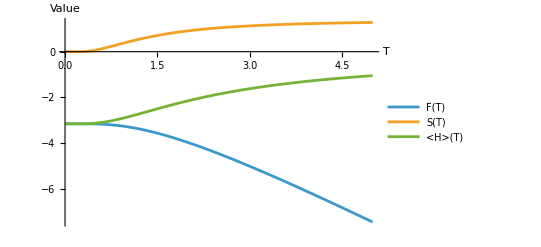

```mathematica
Plot[{freeEnergy[-1.5,-1,T],(*F(T)*)vonNeumannEntropy[rho[-1.5,-1,T]],(*S(T)*)internalEnergy[-1.5,-1,T]           (* <H>(T)*)},{T,0.01,5},PlotRange->All,PlotLegends->{"F(T)","S(T)","<H>(T)"},AxesLabel->{"T","Value"}]
```

```mathematica
Manipulate[Plot[{freeEnergy[a,b,T],vonNeumannEntropy[rho[a,b,T]],internalEnergy[a,b,T]},{T,0.01,5},PlotRange->All,PlotLegends->{"F(T)","S(T)","<H>(T)"},AxesLabel->{"T","Value"}],{a,-3,3,0.01},(*slider para el primer parámetro*){b,-3,3,0.01}   (*slider para el segundo parámetro*)]
```